## Graph

## Basic Examples

An undirected graph:



```mathematica
Graph[{1<->2,2<->3,3<->1}]
```

A directed graph:

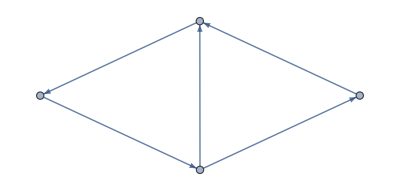

```mathematica
Graph[{1->2,2->3,3->4,4->1,2->4}]
```

Style vertexes and edges:

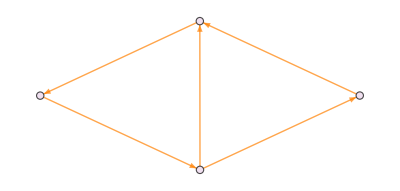

```mathematica
Graph[{1->2,2->3,3->4,4->1,2->4},VertexStyle->LightPurple,EdgeStyle->Orange]
```

Use wrappers to input directly:

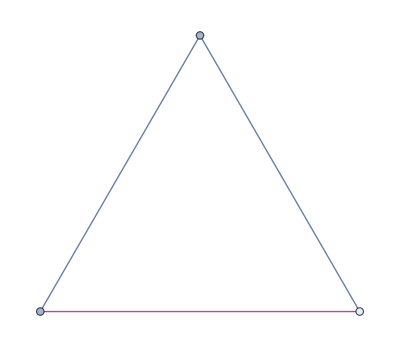

```mathematica
Graph[{1,2,Style[3,LightBlue]},{1<->2,2<->3,Style[3<->1,Purple]}]
```

Label vertices and edges:

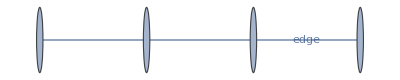

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->4,"edge"]}]
```

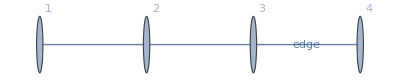

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->4,"edge"]},VertexLabels->"Name"]
```

Use different vertices and edges:

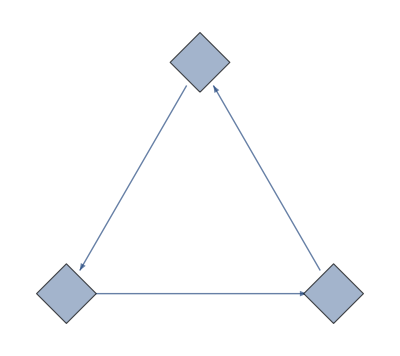

```mathematica
Graph[{1->2,2->3,3->1},VertexShapeFunction->"Diamond",VertexSize->Medium]
```

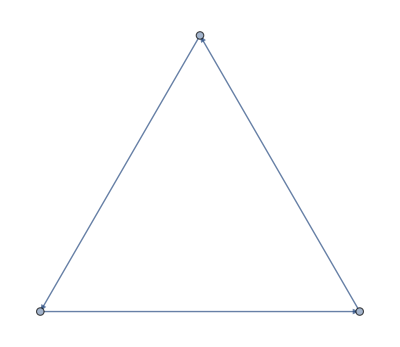

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->"CarvedArcArrow"]
```

## Options

### AnnotationRules

Specify an annotation for vertices:

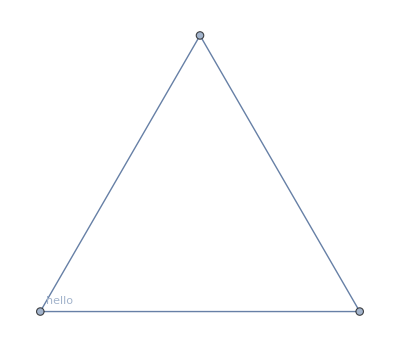

```mathematica
Graph[{1,2,3},{1<->2,2<->3,3<->1},AnnotationRules->{1->{VertexLabels->"hello"}}]
```

Edges:

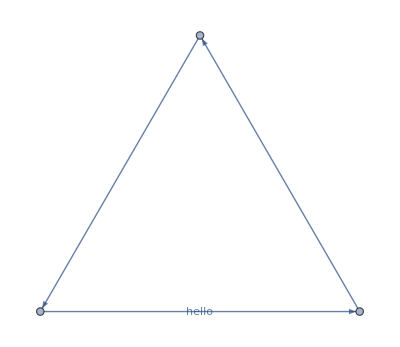

```mathematica
Graph[{1->2,2->3,3->1},AnnotationRules->{1->2->{EdgeLabels->"hello"}}]
```

### DirectedEdges

By default, a directed graph is generated when giving a list of rules:



```mathematica
Graph[{1->2,2->3,3->1}]
```

Use DirectedEdges->False to interpret rules as undirected edges:

```mathematica
Graph[{1->2,2->3,3->1},DirectedEdges->False]
```

-Graphics-

Use DirectedEdge or UndirectedEdge to specify whether a graph is directed or not:

### EdgeLabels

```mathematica
{Graph[{1->2,2->3,3->1}],Graph[{1<->2,2<->3,3<->1}]}
```

{-Graphics-,-Graphics-}

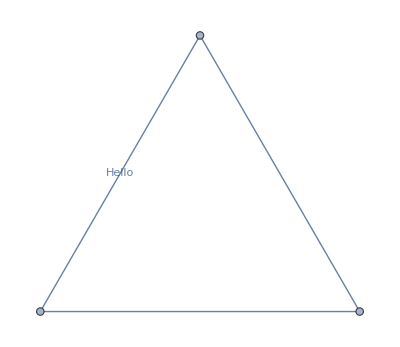

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->"Hello"}]
```

```mathematica
el={1<->2,2<->3,3<->1};
```

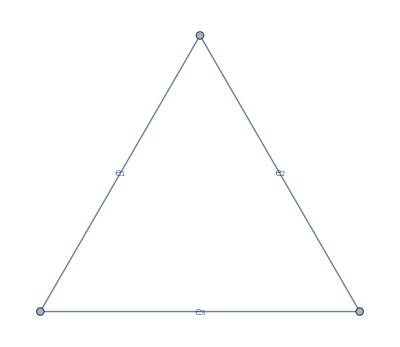

```mathematica
Graph[el,EdgeLabels->Table[el[[i]]->Subscript[e, i],{i,Length[el]}]]
```

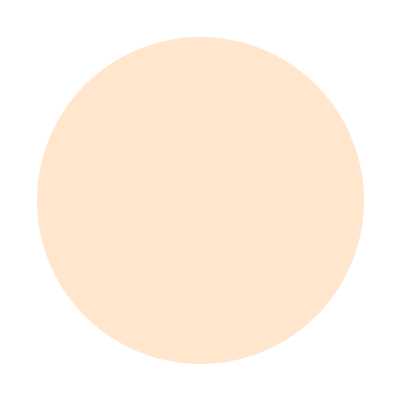
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
edgeLabelImages=Graphics[#,ImageSize->Tiny]&/@{Graphics[{LightOrange,Disk[{3,4}]}],Graphics3D[{Torus[RandomReal[2,{3}],{1,2}]}],PolyhedronData["MathematicaPolyhedron","Image"]}
```

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->-Graphics-,2<->3->-Graphics3D-,3<->1->-Graphics-}]
```

-Graphics-

Use Placed with symbolic locations to control label placement along an edge:

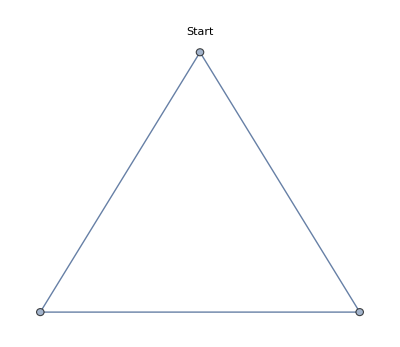
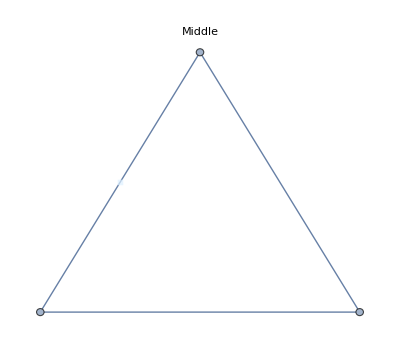
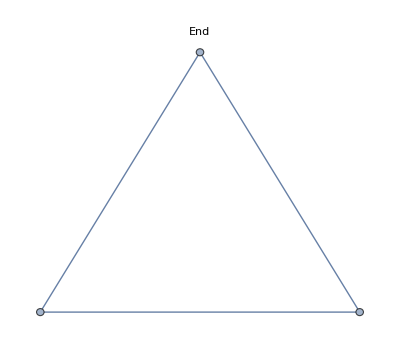

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->Placed[-Graphics-,kp]},PlotLabel->kp],{kp,{"Start","Middle","End"}}]
```

Use explicit coordinates to place labels:

```mathematica
Graphics[{LightBlue,Rectangle[]},ImageSize->50]
```

-Graphics-

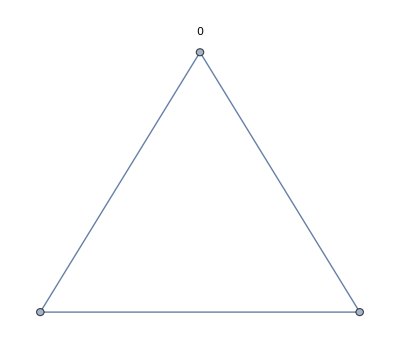
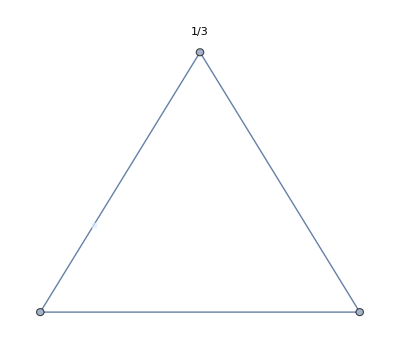
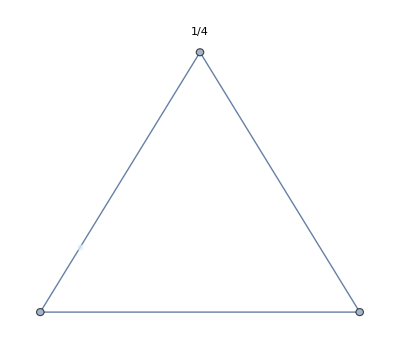

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->Placed[-Graphics-,kp]},PlotLabel->kp,BaselinePosition->Axis],{kp,{0,1/3,1/4}}]
```

Vary positions within the label:

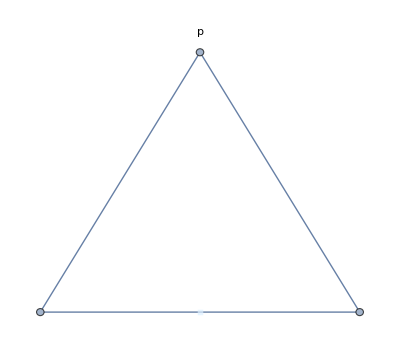
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->3->Placed[-Graphics-,{1/2,kp}]},PlotLabel->p,BaselinePosition->Axis],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place multiple labels using Placed in a wrapper:

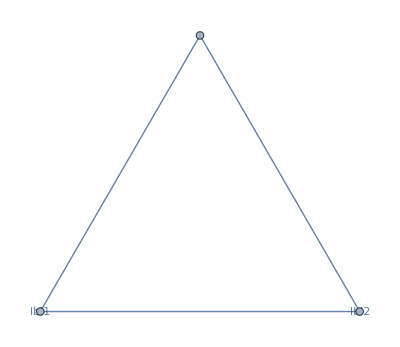

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->1,Placed[{"lbl1","lbl2"},{"Start","End"}]]}]
```

Use automatic labeling by values through Tooltip and StatusArea:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->Placed["Name",StatusArea]]
```

-Graphics-

### EdgeShapeFunction

Get a list of build-in settings for EdgeShapeFunction:

```mathematica
ResourceData["EdgeShapeFunction"]
```

{Arrow,BoxLine,CarvedArcArrow,CarvedArrow,DashedLine,DiamondLine,DotLine,DottedLine,FilledArcArrow,FilledArrow,HalfFilledArrow,HalfFilledDoubleArrow,HalfUnfilledArrow,HalfUnfilledDoubleArrow,Line,ShortCarvedArcArrow,ShortCarvedArrow,ShortFilledArcArrow,ShortFilledArrow,ShortUnfilledArcArrow,ShortUnfilledArrow,UnfilledArcArrow,UnfilledArrow}

Undirected edges including the basic line:

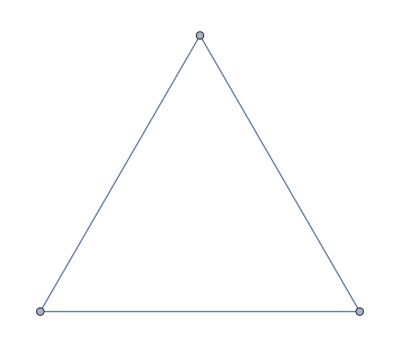

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->"Line"]
```

Lines with different glyphs on the edges:

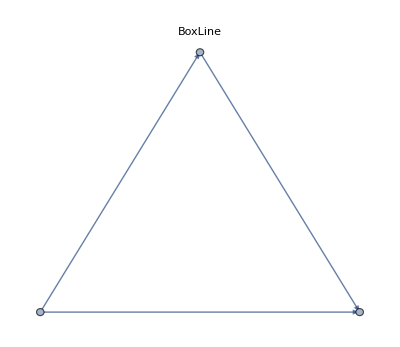
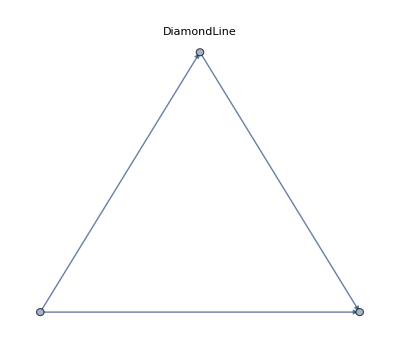
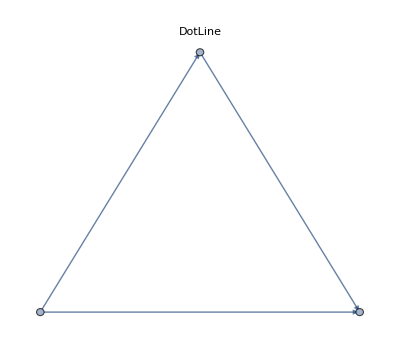

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->kef],{kef,{"BoxLine","DiamondLine","DotLine"}}]
```

Directed edges including solid arrows:

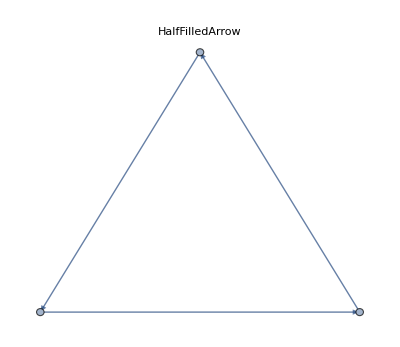
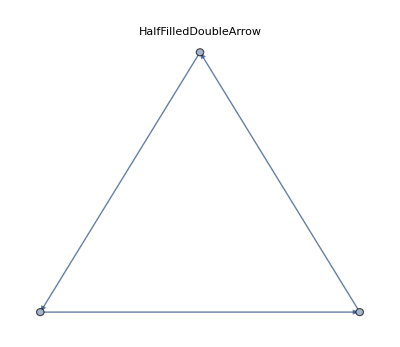
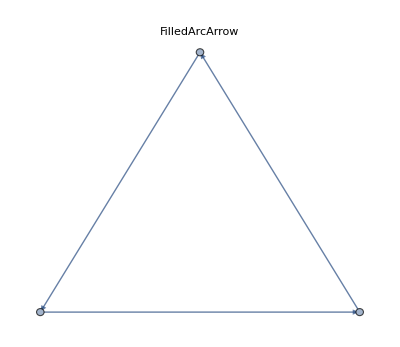
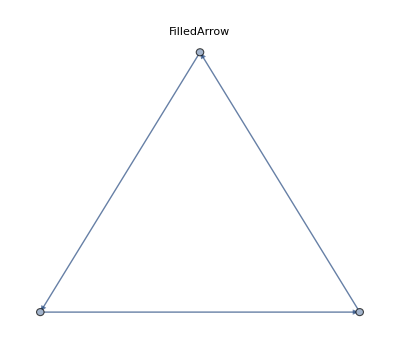
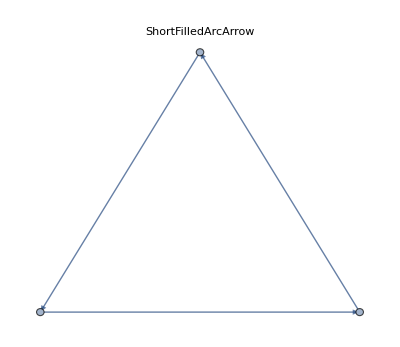
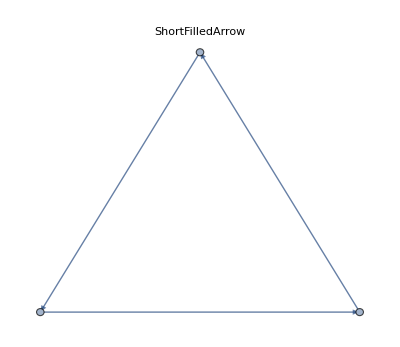

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","FilledArrow"]}]
```

Line arrows:

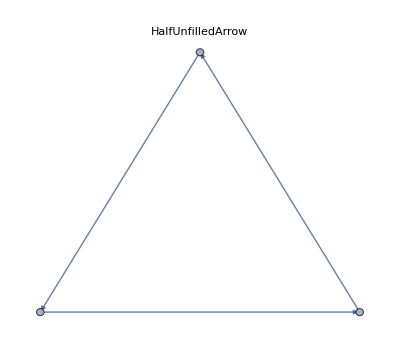
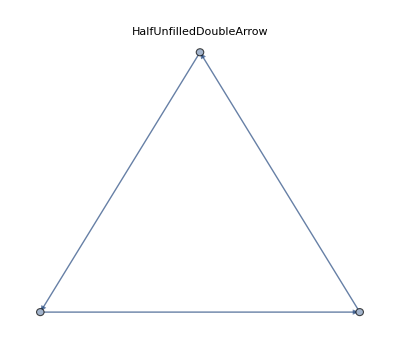
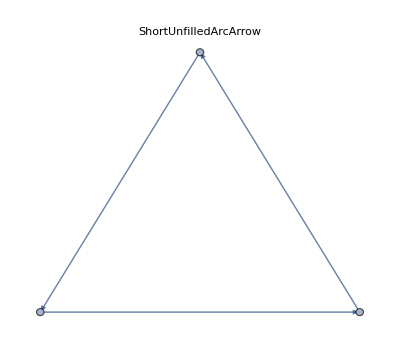
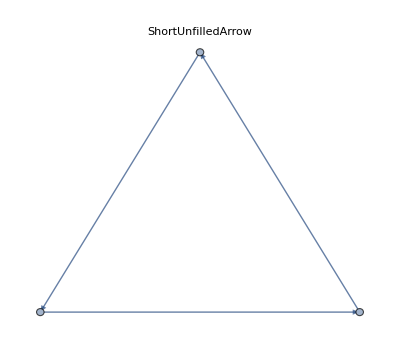
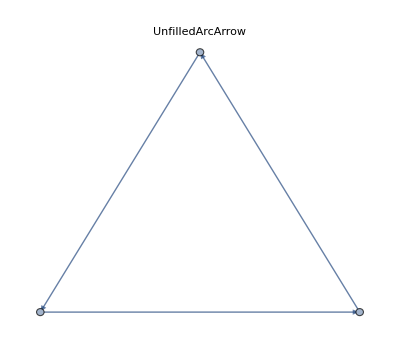
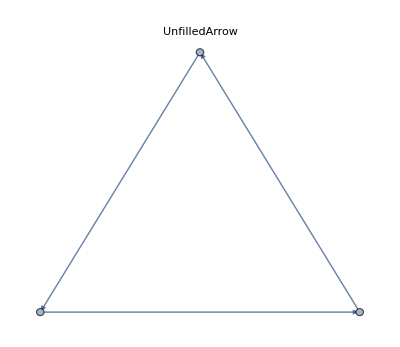

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","UnfilledArrow"]}]
```

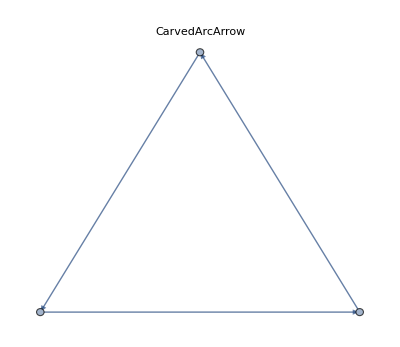
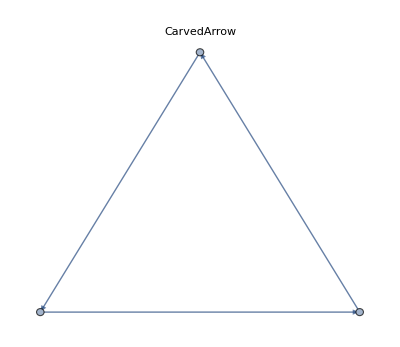
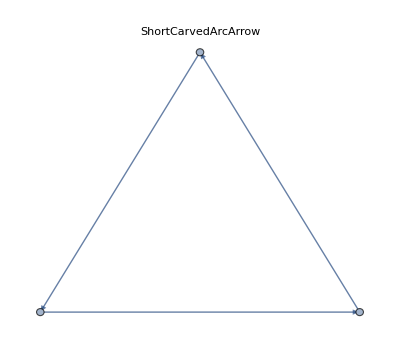
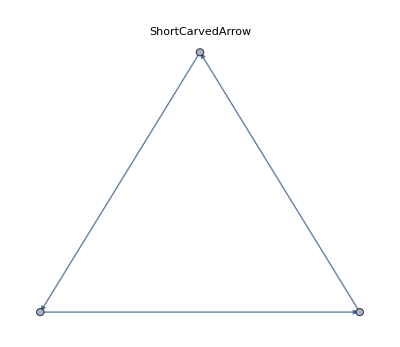

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","CarvedArrow"]}]
```

Specify an edge function for an individual edge:

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->{1->2->"FilledArrow"}]
```

-Graphics-

Combine with a different default edge function:

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->{1->2->"FilledArrow","CarvedArrow"}]
```

-Graphics-

Draw edges by running a program:

```mathematica
ef[pts_List,e_]:=Block[{s=0.015,g=Graphics[Circle[]]},{Arrowheads[{{s,0.33,g},{s,0.67,g}}],Arrow[pts]}]
```

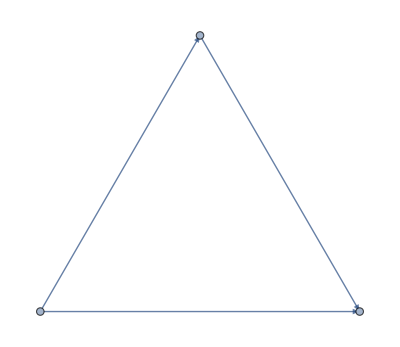

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->ef]
```

EdgeShapeFunction can be combined with EdgeStyle:

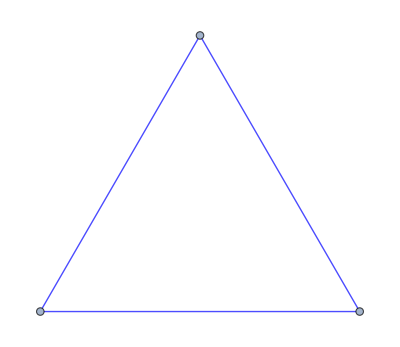

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->(Line[#1]&)]
```

EdgeShapeFunction has higher priority than EdgeStyle:

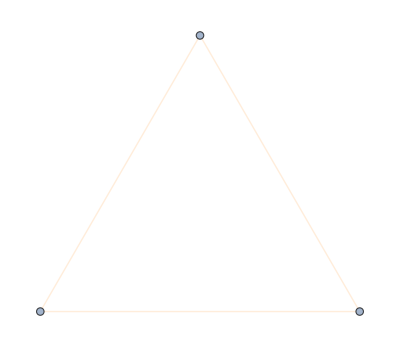

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->({LightOrange,Line[#1]}&)]
```

### EdgeStyle

Style all edges:

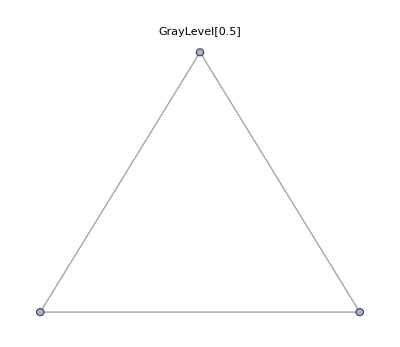
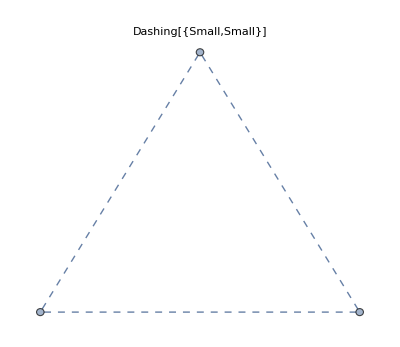
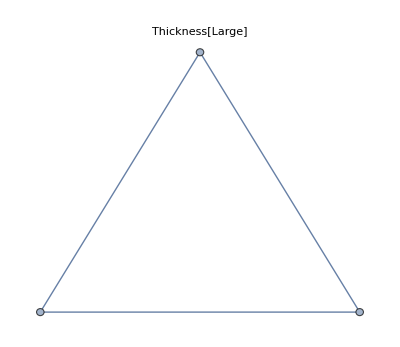

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeStyle->style,PlotLabel->style],{style,{Gray,Dashed,Thick}}]
```

Style individual edges:

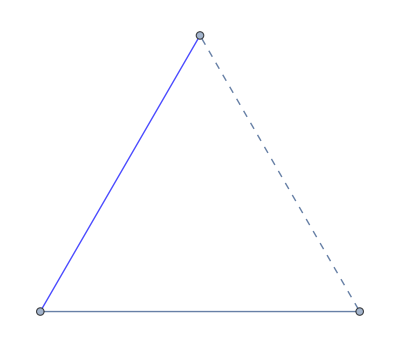

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->{1<->2->Blue,2<->3->Dashed}]
```

EdgeStyle can be combined with EdgeShapeFunction:

```mathematica
efA[el_,___]:=Arrow[el,0.1]
```

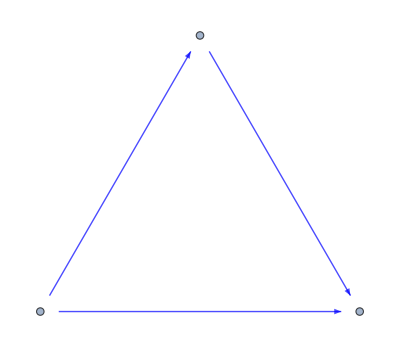

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->efA]
```

EdgeShapeFunction has higher priority than EdgeStyle:

```mathematica
efB[el_,___]:={Red,Arrow[el,0.1]}
```

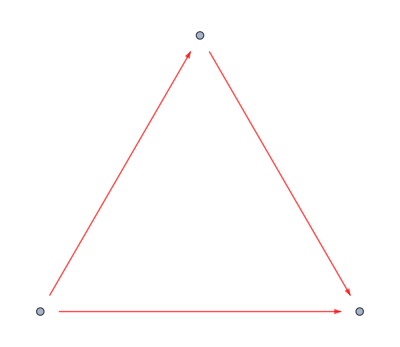

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->efB]
```

EdgeStyle can be combined with BaseStyle:

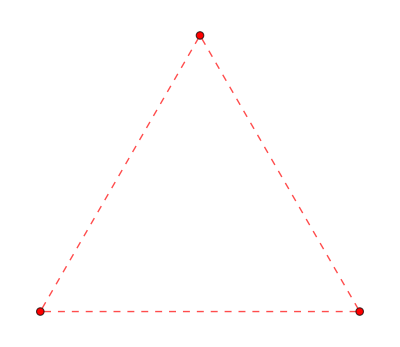

```mathematica
Graph[{1<->2,2<->3,3<->1},BaseStyle->Red,EdgeStyle->Dashed]
```

EdgeStyle has higher priority than BaseStyle:

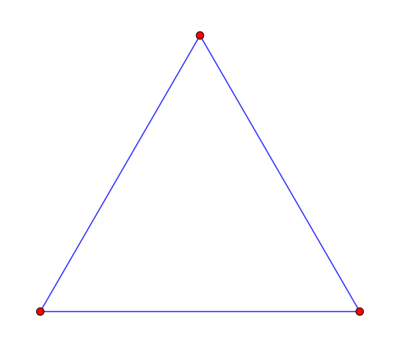

```mathematica
Graph[{1<->2,2<->3,3<->1},BaseStyle->Red,EdgeStyle->Blue]
```

### EdgeWeight

Specify a weight for all edges:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]]//MatrixForm
```

(0 | 3 | 5
3 | 0 | 3
5 | 3 | 0)

Use any numeric expression as a weight:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->{a,b,c}]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,2<->3,3<->1},EdgeWeight->{a,b,c}]]//MatrixForm
```

(0 | a | c
a | 0 | b
c | b | 0)

### GraphHighlight

Highlight the vertex 1:

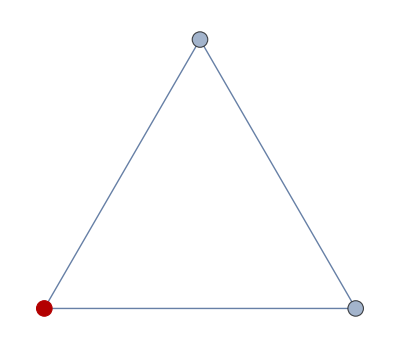

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{1}]
```

Highlight the edge 2<->3:

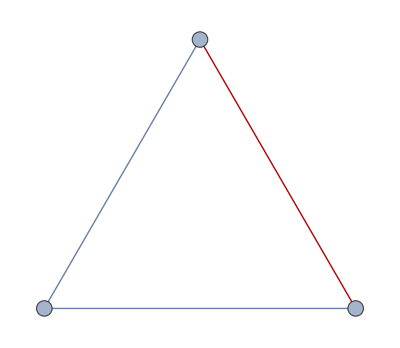

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{2<->3}]
```

Highlight vertices and edges:

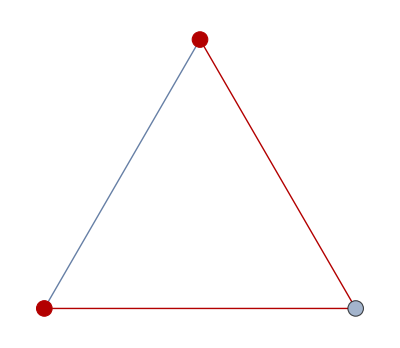

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{1,2,1<->3,2<->3}]
```

### GraphHighlightStyle

Get a list of built-in settings for GraphHighlightStyle:

```mathematica
ResourceData["GraphHighlightStyle"]
```

{Automatic,Dashed,Dotted,Thick,VertexConcaveDiamond,VertexDiamond,VertexTriangle,DehighlightFade,DehighlightGray,DehighlightHide}

Use built-in settings for GraphHighlightStyle:

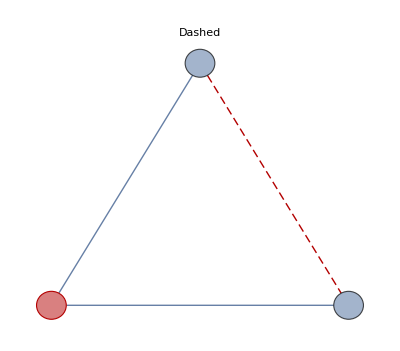
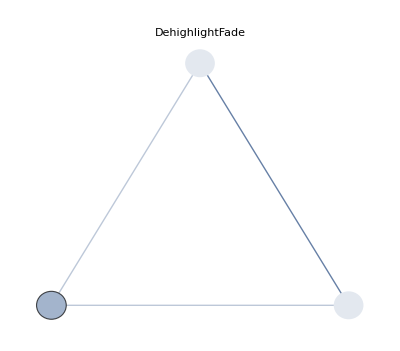
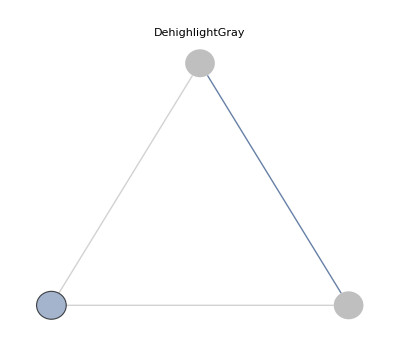
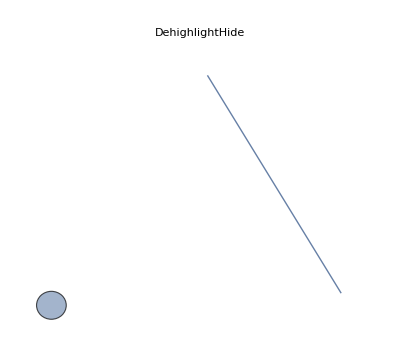
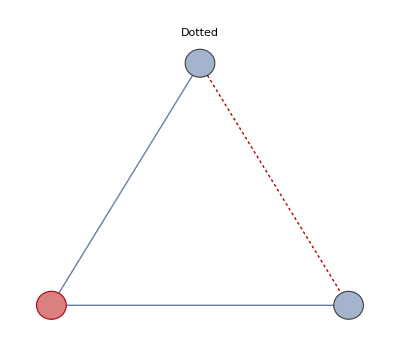
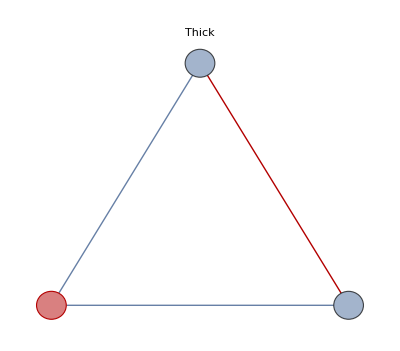
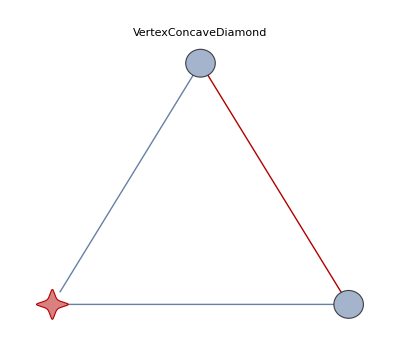
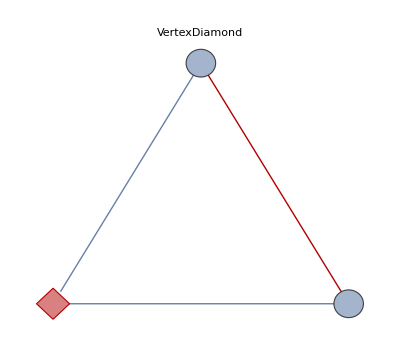

```mathematica
Graph[{1<->2,2<->3,3<->1},GraphHighlight->{1,2<->3},VertexSize->Small,GraphHighlightStyle->#,PlotLabel->#]&/@Complement[ResourceData["GraphHighlightStyle"],{Automatic}]
```

### GraphLayout

By default, the layout is chosen automatically:

```mathematica
Graph[{1<->2,2<->3,3<->1},GraphLayout->Automatic]
```

-Graphics-

Specify layouts on special curves:

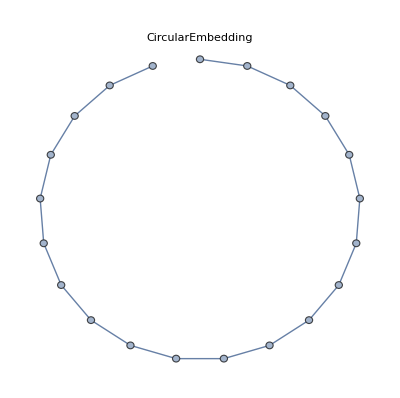
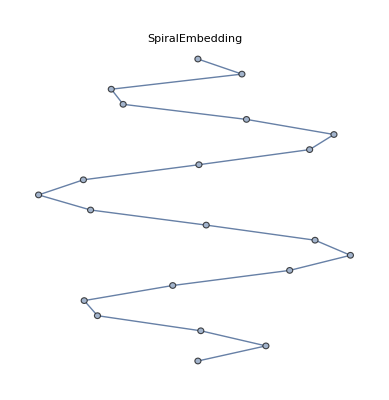

```mathematica
Table[Graph[Table[i<->i+1,{i,20}],GraphLayout->l,PlotLabel->l],{l,{"CircularEmbedding","SpiralEmbedding"}}]
```

Specify layouts that satisfy optimality criteria:

```mathematica
el=EdgeList@GridGraph[{10,10}];
```

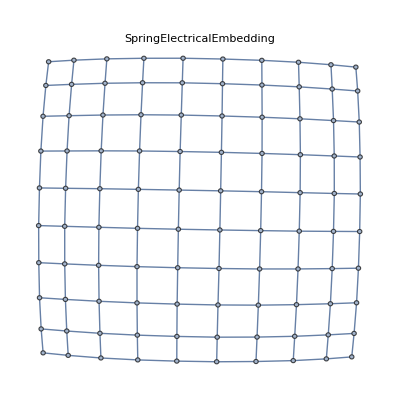
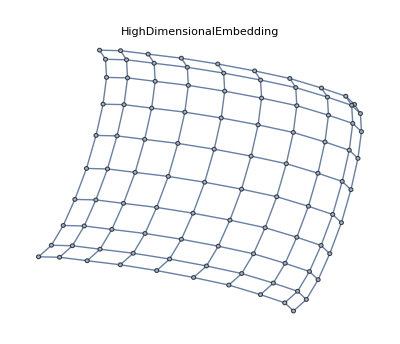
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[el,GraphLayout->l,PlotLabel->Style[l,10]],{l,{"SpringElectricalEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding"}}]
```

VertexCoordinates overrides GraphLayout coordinates:

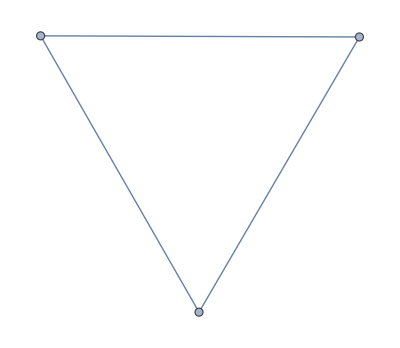
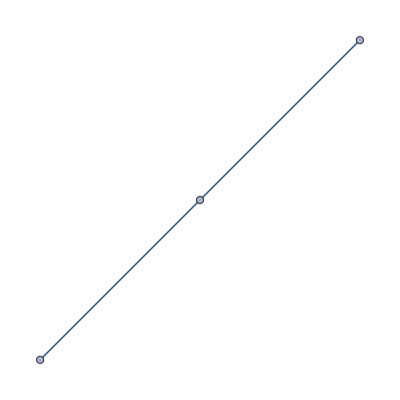

```mathematica
{Graph[{1<->2,2<->3,3<->1},GraphLayout->"SpringElectricalEmbedding"],Graph[{1<->2,2<->3,3<->1},GraphLayout->"SpringElectricalEmbedding",VertexCoordinates->Table[{i,i},{i,0,2}]]}
```